```mathematica
description="Slepton-side cirtual contribution";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

## Assumptions

```mathematica
$Assumptions={
Zql∈Reals,
Zqr∈Reals
};
```

## Get amplitudes

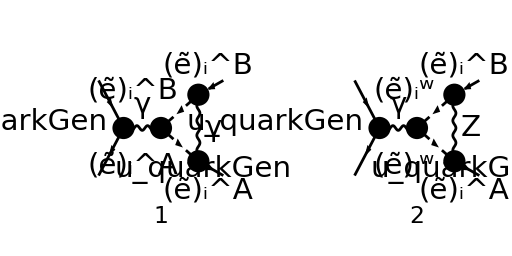

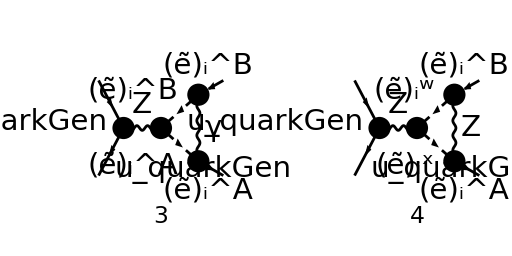

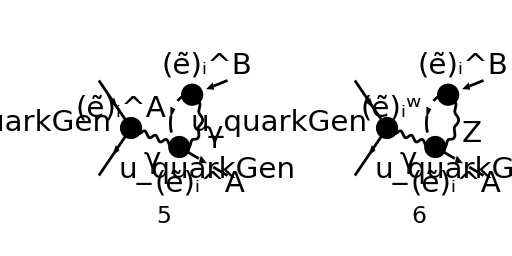

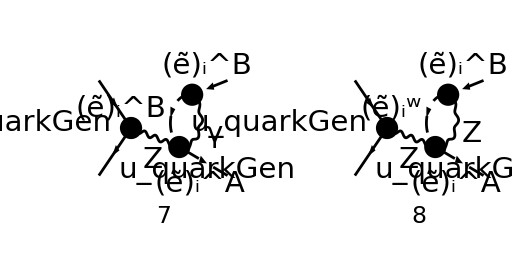

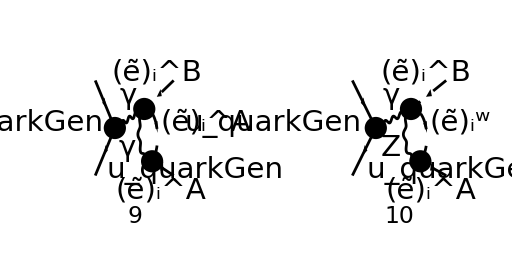

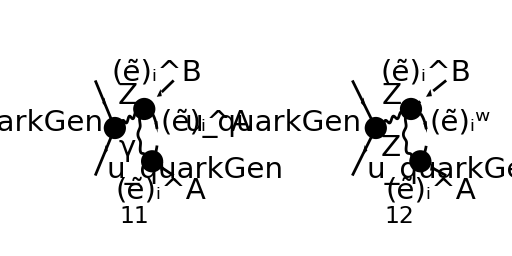

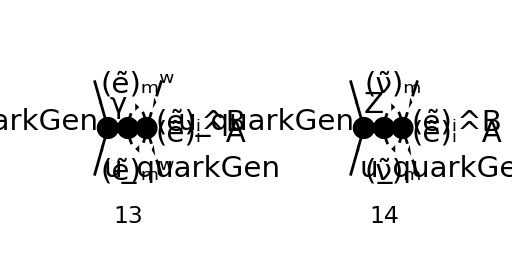

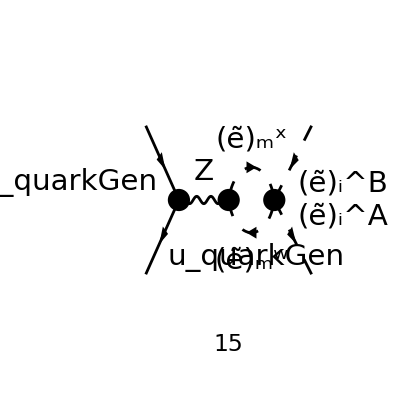

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,Tadpoles, SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6|13|14],F[3|4|11|12],V[3],U[1|2|3|4]}
(*
	S[1,...,6]=Higgs bosons,
	S[13,14]=squarks,
	F[3,4]=quarks (since we only want slepton-side corrections for now),
	F[11,12]=gauginos,
	V[3]=W boson,
	U[1,...,4]=ghosts,
*)
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

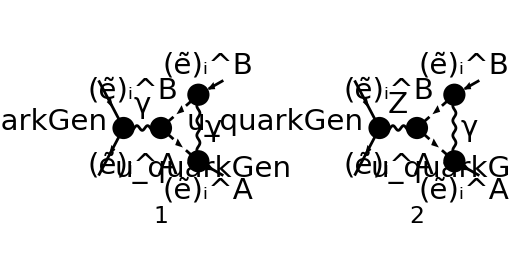

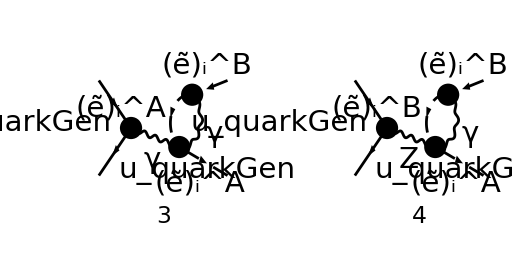

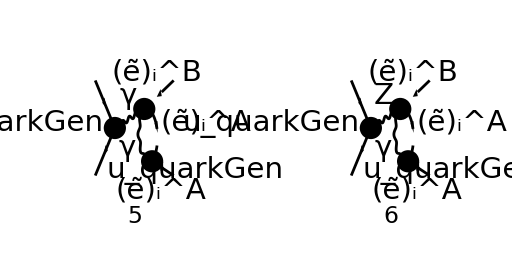

```mathematica
diags[1]=DiagramExtract[diags[0],{1,3,5,7,9,11}];
Paint[
diags[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-((ⅈ (φ(-p_2)).(γ·(-k_1+k_2-2 kloop)).(φ(p_1)) IndexDelta(A,B) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^4 δ_Col1Col2)/(24 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) (k_1+k_2)^2)),-(((φ(-p_2)).((2 ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),-(ⅈ (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-m_l_iA^2).(k_1+kloop)^2 (k_1+k_2)^2),-(((φ(-p_2)).((2 ⅈ (γ·(kloop-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iB^2).(k_1+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 (k_1+k_2)^2),((φ(-p_2)).((2 ⅈ (γ·(kloop-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

## 4-point diagrams

### Only photon parts

```mathematica
M23γlist[0]=Mlist[0][[{3,5}]] 3/2 SMP["e_Q"]
```

{-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_1+kloop)^2),(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_2+kloop)^2)}

```mathematica
M2γ[0]=M23γlist[0][[1]]
M3γ[0]=M23γlist[0][[2]]
```

-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_1+kloop)^2)

(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_2+kloop)^2)

```mathematica
M2γ[1]=M2γ[0]//FeynAmpDenominatorSplit//ReplaceAll[#,{FeynAmpDenominator[PropagatorDenominator[Momentum[kloop,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[kloop,D],MSf[B,2,i]]]}]&
```

-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_1+kloop)^2 (kloop^2-m_l_iB^2))

```mathematica
M23γ[0]=M2γ[1]+M3γ[0]//FeynAmpDenominatorSplit
```

(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_2+kloop)^2 (kloop^2-m_l_iA^2))-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_1+kloop)^2 (kloop^2-m_l_iB^2))

```mathematica
M23γ[1]=M23γ[0]//TID[#,kloop,ToPaVe->True]&
```

-(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) A_0(m_l_iA^2) (φ(-p_2)).(γ·k_2).(φ(p_1)))/(16 π^2 k_2^2 (k_1+k_2)^2)+(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) A_0(m_l_iB^2) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(16 π^2 k_1^2 (k_1+k_2)^2)+(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2) (φ(-p_2)).(γ·k_2).(φ(p_1)))/(16 π^2 k_2^2 (k_1+k_2)^2)+-(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(16 π^2 k_1^2 (k_1+k_2)^2)

```mathematica
M23γ[2]=M23γ[1]//PaVeOrder//Simplify
```

1/(16 π^2 k_1^2 k_2^2 (k_1+k_2)^2)e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (k_1^2 (φ(-p_2)).(γ·k_2).(φ(p_1)) ((m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2)-A_0(m_l_iA^2))+k_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) (A_0(m_l_iB^2)-(m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2)))

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M23γ[3]=M23γ[2]
```

1/(16 π^2 (k_1+k_2)^2 m_l_iA^2 m_l_iB^2)e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iA^2 (A_0(m_l_iB^2)-4 m_l_iB^2 B_0(m_l_iB^2,0,m_l_iB^2)) (φ(-p_2)).(γ·k_1).(φ(p_1))+m_l_iB^2 (4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)-A_0(m_l_iA^2)) (φ(-p_2)).(γ·k_2).(φ(p_1)))

```mathematica
M23γHand[0]=SMP["e"]^4SMP["e_Q"]SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]] IndexDelta[A,B]FAD[k1+k2] /(8 Pi^2) SpinorVBarD[p2].GAD[μ].SpinorUD[p1] (2 FVD[k2,μ] B0[SPD[k2],MSf[A,2,i]^2,0]-2FVD[k1,μ] B0[SPD[k1],MSf[B,2,i]^2,0]-1/2 FVD[k2,μ] A0[MSf[A,2,i]^2]/MSf[A,2,i]^2 + 1/2 FVD[k1,μ] A0[MSf[B,2,i]^2]/MSf[B,2,i]^2)//Contract//PaVeOrder//Simplify
```

1/(16 π^2 (k_1+k_2)^2 m_l_iA^2 m_l_iB^2)e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iA^2 (A_0(m_l_iB^2)-4 m_l_iB^2 B_0(m_l_iB^2,0,m_l_iB^2)) (φ(-p_2)).(γ·k_1).(φ(p_1))-m_l_iB^2 (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)) (φ(-p_2)).(γ·k_2).(φ(p_1)))

```mathematica
FCCompareResults[{M23γ[3]},{M23γHand[0]},
Text->{"Compare to hand calculations:","Correct!","Wrong!"},
Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Correct!

### Only Z-boson parts

```mathematica
M23Zlist[0]=Mlist[0][[{4,6}]]//ZSimplify
```

{(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_1)).(γ̄)^7+Z_q_R (γ·(kloop-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iB^2).(k_1+kloop)^2),-(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_2)).(γ̄)^7+Z_q_R (γ·(kloop-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iA^2).(k_2+kloop)^2)}

```mathematica
M23Z[0]=Total[M23Zlist[0]]
```

(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_1)).(γ̄)^7+Z_q_R (γ·(kloop-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iB^2).(k_1+kloop)^2)-(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_2)).(γ̄)^7+Z_q_R (γ·(kloop-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iA^2).(k_2+kloop)^2)

```mathematica
M23Z[1]=M23Z[0]//TID[#,kloop,ToPaVe->True]&//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 Z_l_i^AB (k_1^2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (A_0(m_l_iA^2)-(m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2))+k_1^2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (A_0(m_l_iA^2)-(m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2))-(k_2^2 (A_0(m_l_iB^2)-(m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))))/(8 π^2 k_1^2 k_2^2 (cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M23ZHand[0]=- SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]SMP["e"]^4 FAD[{k1+k2,SMP["m_Z"]}]  ZliAB /(8 Pi^2 SMP["sin_W"]^2 SMP["cos_W"]^2)(SpinorVBarD[p2].GAD[μ].(2 Zql GAD[7]+2Zqr GAD[6]).SpinorUD[p1])(2 FVD[k2,μ] B0[SPD[k2],MSf[A,2,i]^2,0]-2 FVD[k1,μ] B0[SPD[k1],MSf[B,2,i]^2,0]-1/2 FVD[k2,μ] A0[MSf[A,2,i]^2]/MSf[A,2,i]^2+1/2 FVD[k1,μ] A0[MSf[B,2,i]^2]/MSf[B,2,i]^2)
```

-((e^4 δ_Col1Col2 Z_l_i^AB v̄(p_2).γ^μ.(2 (γ̄)^7 Z_q_L+2 (γ̄)^6 Z_q_R).u(p_1) (2 k_2^μ B_0(m_l_iA^2,0,m_l_iA^2)-2 k_1^μ B_0(m_l_iB^2,0,m_l_iB^2)-(k_2^μ A_0(m_l_iA^2))/(2 m_l_iA^2)+(k_1^μ A_0(m_l_iB^2))/(2 m_l_iB^2)))/(8 π^2 (cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2)))

```mathematica
M23ZHand[1]=M23ZHand[0]//Contract//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 Z_l_i^AB (-(m_l_iA^2 (A_0(m_l_iB^2)-4 m_l_iB^2 B_0(m_l_iB^2,0,m_l_iB^2)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))+m_l_iB^2 Z_q_L (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))+m_l_iB^2 Z_q_R (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))))/(8 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))

```mathematica
M23Ztest[0]=M23Z[1]//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 Z_l_i^AB (-(m_l_iA^2 (A_0(m_l_iB^2)-4 m_l_iB^2 B_0(m_l_iB^2,0,m_l_iB^2)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))+m_l_iB^2 Z_q_L (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))+m_l_iB^2 Z_q_R (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2)) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))))/(8 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))

```mathematica
FCCompareResults[{M23Ztest[0]},{M23ZHand[1]},
Text->{"Compare to hand calculations:","Correct!","Wrong!"},
Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Correct!

## Triangle diagrams

```mathematica
M1γ[0]=Mlist[0][[1]] 3/2 SMP["e_Q"]
```

```mathematica
M1Z[0]=Mlist[0][[2]]
```

```mathematica
M1Z[1]=M1Z[0]//ZSimplify
```

```mathematica
M1Z[1]//DiracSubstitute67(*Easier to compare to hand calculations*)
```

```mathematica
M1[0]=M1γ[0]+M1Z[1]
```

```mathematica
M1[1]=M1[0]/.{Momentum[-k1+k2-2 kloop,D]->Momentum[-k1-2kloop+p1+p2-k1,D]}
```

```mathematica
M1[2]=M1[1]//DiracSimplify//Simplify
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=0;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M1[3]=M1[2]//TID[#,kloop,ToPaVe->True]&//FeynAmpDenominatorExplicit//DiracSimplify//Simplify
```

### Testing just the photon diagram

```mathematica
M1γ[1]=M1γ[0]/.{Momentum[-k1+k2-2kloop,D]->Momentum[-k1+p1+p2-k1-2kloop,D]}
```

```mathematica
M1γ[2]=M1γ[1]//DiracSimplify//Simplify
```

```mathematica
M1γ[3]=M1γ[2]//TID[#,kloop,ToPaVe->True]&//Simplify
```

```mathematica
M1γ[3]//Collect2[#,A0,IsolateNames->KK]&
```

```mathematica
M1γ[3]//Collect2[#,B0,IsolateNames->KK]&
```

```mathematica
M1γ[3]//Collect2[#,C0,IsolateNames->KK]&
```

```mathematica
M1γ[3]//Collect2[#,D0,IsolateNames->KK]&
```

```mathematica
KK[1594]//FRH
```

```mathematica
C0[SPD[k1],SPD[k2],SPD[k1+k2],MSf[B,2,i]^2,0,MSf[A,2,i]^2]//ToPaVe2
```

```mathematica
testPV[0]=FAD[{k,m0},{k+p1,m1}]+FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2}]
```

```mathematica
testPV[1]=testPV[0]//TID[#,k]&
```

```mathematica
testPV[2]=testPV[0]//TID[#,k,ToPaVe->True]&
```

```mathematica
testPV[1][[2]]
%//TID[#,k,ToPaVe->True,UsePaVeBasis->False]&
```

```mathematica
expr=FAD[{k,m1},k-p1]
expr//TID[#,k]&
expr//TID[#,k,ToPaVe->True]&
```

```mathematica
expr=FAD[{k,m1},k+p1]
expr//TID[#,k]&
expr//TID[#,k,ToPaVe->True]&
```

```mathematica
int=FAD[{k,m},k-Subscript[p,1],k-Subscript[p,2]] FVD[k,μ]
```

```mathematica
int//TID[#,k]&//Simplify
```

```mathematica
int//TID[#,k,ToPaVe->True]&
```

```mathematica
FCClearScalarProducts[];
```

```mathematica
int=FAD[{k,m0},{k+p1,m1},{k+p2,m2}]
int//TID[#,k]&
int//TID[#,k,ToPaVe->True]&
```

```mathematica
int=FAD[{k,m0},{k-p1,m1},{k-p2,m2}]
int//TID[#,k]&
int//TID[#,k,ToPaVe->True]&
```

```mathematica
int=FAD[{k,m0},{k+p1,m1}]
int//TID[#,k]&
int//TID[#,k,ToPaVe->True]&
```

```mathematica
int=FAD[{k,m0},k+p1]
int//TID[#,k]&
int//TID[#,k,ToPaVe->True]&
```

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,WFCorrections,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6|13|14],F[3|4|11|12],V[3],U[1|2|3|4]}
];
Paint[
diags,
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
diags[1]=DiagramExtract[diags[0],{1,3,5,7,9,11}];
Paint[
diags[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
Contract->False,
LorentzIndexNames->{μ,ν},
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

```mathematica
M3γ[0]=Mlist[0][[5]] 3/2 SMP["e_Q"]
```

```mathematica
M3γ[0]//Contract
```